# 黑洞吸积盘图片

## 测地线方程

计算测地线方程。

```mathematica
<<EinsteinSummation`
```

Einstein Summation Package Guide »
Einstein Summation Tutorial »

```mathematica
Clear@Rs
SetVars[{t,r,θ}];
$constants={Rs};
SetMetric[DiagonalMatrix[{-(1-Rs/r),1/(1-Rs/r),r^2}]]
AddTensorToDataset["v^ν",{tt'[τ],rr'[τ],θθ'[τ]}]
```

```mathematica
expr=EvaluateEinsteinSummation["-Γ_νσ^μ v^νv^σ"]["Value"]/.r->rr[τ]//FullSimplify
```

{(rr'[τ] tt'[τ])/(rr[τ]-rr[τ]^2),(rr[τ]^2 rr'[τ]^2-(-1+rr[τ])^2 tt'[τ]^2)/(2 (-1+rr[τ]) rr[τ]^3)+(-1+rr[τ]) θθ'[τ]^2,-(2 rr'[τ] θθ'[τ])/rr[τ]}

## 构造 {r,θ}→{θ_0,θ_1,Δt} 关系（2D 光追）

预先设定接受者距离中心的距离R0，一个比较合适的观察者位置是6Rs处，即两倍的最内层稳定圆周轨道（ISCO）处。

{r,θ} 是发射点坐标
θ_0 是接收者接到光的方向与r方向的夹角——ReceiveAngleFunction
θ_1 是被接受者接收到的这一束光，在发出时与r方向夹角——EmitAngleFunction
Δt 是从发出到接收经过的坐标时——DelayFunction

这里只考虑光线绕了小于1.5圈的情况（可以大于半圈）
之所以不考虑转了1.5圈以上的是因为计算表明，转1.5圈以上的时候，其强度至少30倍的弱于转小于一圈的（别的因子影响不大，但是强度Part I一节中计算的因子部分对转角比较敏感），那其实就是看不见了咯……但是如果转1.2圈或者什么，也就是比转0.x圈弱了两三倍，还是非常值得考虑的。

```mathematica
$HistoryLength=0;
```

```mathematica
Rs=1;
R0=6Rs;
Rmax=6Rs+1.*^-6;
```

θ0是接收角

```mathematica
parfunc=ParametricNDSolveValue[{{tt''[τ],rr''[τ],θθ''[τ]}=={(rr'[τ] tt'[τ])/(rr[τ]-rr[τ]^2),(rr[τ]^2 rr'[τ]^2-(-1+rr[τ])^2 tt'[τ]^2)/(2 (-1+rr[τ]) rr[τ]^3)+(-1+rr[τ]) θθ'[τ]^2,-(2 rr'[τ] θθ'[τ])/rr[τ]},{tt'[0],rr'[0],θθ'[0]}=={1/(1-Rs/R0),-Cos[θ0],Sqrt[1/(1-Rs/R0)]/R0 Sin[θ0]},{tt[0],rr[0],θθ[0]}=={0,R0,0},WhenEvent[1.01Rs≥rr[τ]||rr[τ]≥Rmax||θθ[τ]≥3.1Pi,"StopIntegration"]},{tt[τ],rr[τ],θθ[τ]},{τ,0,1000},{θ0}];
```

对不同的θ0，反向追光，记录光线轨迹上的{θ_0,θ_1,Δt}。
为了精度和方便考虑，我们这里认为所有物体都在2.5~5.5 Rs之内（观察者认为在6 Rs处，ISCO于3Rs处)。

```mathematica
datp=Catenate@Table[With[{pf=parfunc[θ]},With[{τmax=pf[[1,0,1,1,2]],df=D[Rest@pf,τ],f=Rest@pf},Block[{τ=Range[RandomReal[{0,τmax/500}],τmax,τmax/500]},Select[Thread[(Thread@f->Thread@{θ,ArcTan[-df[[1]],df[[2]] f[[1]] Sqrt[1-Rs/f[[1]]]],pf[[1]]})],2.4Rs<#[[1,1]]<5.6Rs&&-0.05Pi<#[[1,1]]<3.08Pi&]]]],{θ,Range[-2.5Degree,80Degree,1Degree]~Join~Range[20.2Degree,28.2Degree,0.5Degree]~Join~Range[23.025Degree,24.05Degree,0.05Degree]~Join~Range[23.2825Degree,23.4Degree,0.005Degree]~Join~Range[23.28525Degree,23.30025Degree,0.001Degree]}];
datp=First/@GatherBy[datp,Floor[#[[1]]/{0.01Rs,1Degree}]&];
```

绘制采样点（太密了没必要，太疏了结果不精确），这里限制精度的主要是下一部分中的反向追踪那块。

25793

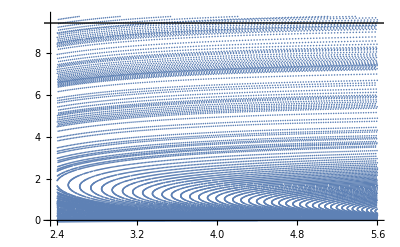

```mathematica
Length@datp[[;;,1]]
ListPlot[datp[[;;,1]],Epilog->{Line[{{0,3Pi},{10,3Pi}}]},PlotRange->Full]
```

插值函数

```mathematica
ReceiveAngleFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,1]]}],InterpolationOrder->1];
EmitAngleFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,2]]}],InterpolationOrder->1];DelayFunction=Interpolation[Thread[{datp[[;;,1]],datp[[;;,2,3]]}],InterpolationOrder->1];
```

测试、画图

```mathematica
Through[{ReceiveAngleFunction,EmitAngleFunction,DelayFunction}[4,40Degree]]
```

{0.735682,1.26992,4.54343}

```mathematica
Plot3D[#[x,y],{x,3,5.5},{y,0,3Pi}]&/@{ReceiveAngleFunction,EmitAngleFunction,DelayFunction}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 强度 Part 1

这一步我们只考虑由于“距离”远近带来的强度衰减。
强度与距离远近的关系在正常平直的时空中是二次方反比，这是因为假如我们摆个圆盘，那圆盘距离发光点越远，圆盘相对发光点的张角就越小，这个关系是二次方。这里光线是弯曲的，所以关系可能很复杂，我们只能数值求解。

我们需要计算两个方向上的光发散。垂直平面和平面内。垂直平面可以直接通过前面得到的θ_0,θ_1计算，而平面内则要反向追踪光线获得。原理如附图。

```mathematica
parfuncrev=ParametricNDSolveValue[{{tt''[τ],rr''[τ],θθ''[τ]}=={(rr'[τ] tt'[τ])/(rr[τ]-rr[τ]^2),(rr[τ]^2 rr'[τ]^2-(-1+rr[τ])^2 tt'[τ]^2)/(2 (-1+rr[τ]) rr[τ]^3)+(-1+rr[τ]) θθ'[τ]^2,-(2 rr'[τ] θθ'[τ])/rr[τ]},{tt'[0],rr'[0],θθ'[0]}=={1/(1-Rs/R1),Cos[θ0],-Sqrt[1/(1-Rs/R1)]/R1 Sin[θ0]},{tt[0],rr[0],θθ[0]}=={0,R1,θ1},WhenEvent[θθ[τ]==0,"StopIntegration"]},{tt[τ],rr[τ],θθ[τ]},{τ,0,100},{θ0,R1,θ1}];
```

验证反向光追的精度，蓝线为正向光追，绿线为反向光追。

23.301

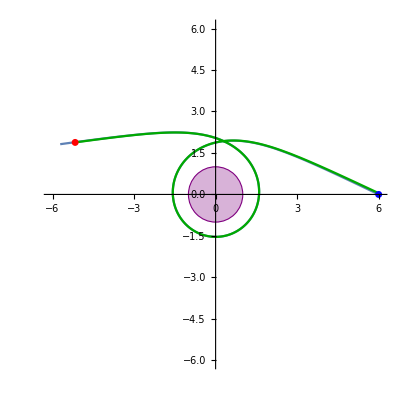

```mathematica
{pr,pt}={5.5,520Degree};
ReceiveAngleFunction[pr,pt]/Degree
pf=parfunc[ReceiveAngleFunction[pr,pt]];
τmax=pf[[1,0,1,1,2]];

fig1=ParametricPlot[Evaluate[#2{Cos[#3],Sin[#3]}&@@pf],{τ,0,τmax},Epilog->{Purple,Opacity@.3,EdgeForm@Directive[Purple,Opacity@1],Disk[],Red,AbsolutePointSize@5,Opacity@1,Point[pr{Cos[pt],Sin[pt]}],Blue,Point[{R0,0}]},PlotRange->{{-1,1},{-1,1}}1.01Rmax];

pf=parfuncrev[EmitAngleFunction[pr,pt],pr,pt];
τmax=pf[[1,0,1,1,2]];
fig2=ParametricPlot[Evaluate[#2{Cos[#3],Sin[#3]}&@@pf],{τ,0,τmax},PlotRange->{{-1,1},{-1,1}}Rmax,PlotStyle->Darker@Green];
Show[fig1,fig2]
```

打点，逐个点计算光强度因子。

```mathematica
Δϕ=1.*^-5;
```

```mathematica
intensity=Catenate@Table[{{R,θ},R0^2 With[{θ=Abs[θ]},Abs[Sin[EmitAngleFunction[R,θ]]/(R0 Sin[θ])]*(Δϕ/(Sin[ReceiveAngleFunction[R,θ]]* Subtract@@(With[{f=parfuncrev[EmitAngleFunction[R,θ]+# Δϕ,R,θ][[2,0]]},f@f[[1,1,-1]]]&/@{-1,1})))]},{R,2.45Rs,5.55Rs,0.02Rs},{θ,-3Degree,543Degree,2Degree}];
```

```mathematica
IntensityFunction1=Interpolation[intensity];
```

相对亮度分布，假如离源较近的话基本和平直空间一致，呈平方反比律。背面光强极强至发散（引力透镜），绕一圈的话强度就很低了。

```mathematica
Show[ListContourPlot[Join[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,0<#[[1,2]]<1.2Pi&],Append[#[[1]]{Cos[#[[2]]],-Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,0<#[[1,2]]<.5Pi&]],RegionFunction->Function[{x,y},y>0&&(2.5Rs)^2<x^2+y^2<(5.5Rs)^2],PlotRange->{-10,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-10,6,.5],InterpolationOrder->3],
ListContourPlot[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,.8Pi<#[[1,2]]&],RegionFunction->Function[{x,y},y<0&&(2.5Rs)^2<x^2+y^2<(5.5Rs)^2],PlotRange->{-10,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-10,6,.5],InterpolationOrder->3],Epilog->{AbsoluteThickness@3,Black,Line[{{0,0},{10,0}}]}]
```

-Graphics-

```mathematica
ListContourPlot[Append[#[[1]]{Cos[#[[2]]],Sin[#[[2]]]},Log2@#2]&@@@Select[intensity,1.05Pi<#[[1,2]]<3.05Pi&],RegionFunction->Function[{x,y},-.5Pi<ArcTan[x,y]<Pi&&(2.5Rs)^2<x^2+y^2<(5.5Rs)^2],PlotRange->{-20,6},ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][(#+10)/16]&),Contours->Range[-20,6,.5],InterpolationOrder->3]
```

-Graphics-

平方反比律验证，在观测者和源比较接近的时候（这里取距离小于3 Rs）和平方反比预测一致。
横轴：平方反比律的预测，纵轴：实际结果

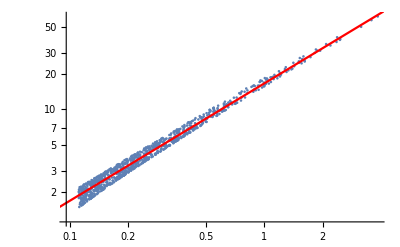

```mathematica
samplereg=ImplicitRegion[x^2+y^2≤(5.5Rs)^2&&(6-x)^2+y^2≤(3 Rs)^2&&y>0,{x,y}];
samples={1/((6Rs-#1)^2+#2^2),IntensityFunction1[Norm[{#1,#2}],ArcTan[#1,#2]]}&@@@RandomPoint[samplereg,1000];
fit=FindFit[samples,k x,k,x];
Show[ListLogLogPlot[samples],Plot[Log[k]+x/.fit,{x,-3,3},PlotStyle->Red]]
```

## 频移

输入{R1,θ,ϕ},{vr,vθ,vϕ},T,I，我们希望得到新角度&新光谱&新光谱强度。

很显然，观测到的角度为{θ_obs,ϕ_obs}={ReceiveAngleFunction[R1,θ],ϕ}
但是颜色、强度和被观测到的时间还有待商榷

先看颜色，两部分，发出时频移（狭相）和传播时频移（广相）

发出时ω_0=ω·v，接收到ω_1=ω√(g_00'/g_00)，其中ω是刚发射出来时从地系看到的频率。

先写两个很好用的辅助函数，第一个计算固定dr/dt,dθ/dt,dϕ/dt（注意，是dt）的时候其绝对速度β
另一个则是计算光线方向与速度方向夹角的：

```mathematica
Calcβ[{R1_,θ_,ϕ_},{vr_,vθ_,vϕ_}]:=Sqrt[vr^2/(1-Rs/R1)+(R1 vθ)^2+(R1 Sin[θ]vϕ)^2]/Sqrt[1-Rs/R1]
```

Input should be a list.

```mathematica
CalcCosAngle[{R1_,θ_,ϕ_},{vr_,vθ_,vϕ_}]:=With[{v={vr/Sqrt[1-Rs/R1],R1 vθ,R1 Sin[θ]vϕ}},MapThread[With[{θ0=EmitAngleFunction[R1,#1]},
With[{vnormed=MapThread[Normalize@*List,v]},MapThread[Dot,{vnormed,Thread@{Cos[θ0],#2 Sin[θ0],0}},1]]]&,{{θ,2Pi-θ,2Pi+θ},{-1,1,-1}}]]
```

```mathematica
CalcCosAngle[{4,{30Degree,20Degree},0},{{.2,.03},{.1,.2},{.3,.1}}]
```

```mathematica
FrequencyMult[R1_,β_,cos_]:=Sqrt[(1-Rs/R1)/(1-Rs/R0)]*Sqrt[1-β^2]/(1-β cos)
```

## 强度 Part 2

在我们计算最终被观测到的强度时有两个部分：
1. 发出者发出的时候强度分布（和速度及发射角有关）
这其实是在讨论光发出的立体角将如何重新分布，如果发射体本征系中θ变成了地系下的θ’，那么θ方向角度变为dθ’/dθ倍，而ϕ方向变为sin(θ’)/sin(θ)倍，故在单位立体角内由该效应会加强dθ/dθ’*sin(θ)/sin(θ’)倍。

2. 由于频移/光子密度改变带来的强度改变，由于频率改变和光子密度改变其实是一个事情，所以两个合起来恰好是FrequencyMult^2
3. 广义相对论带来的透镜效应（也就是前面强度 Part 1中讨论的）

为了避免重复计算，实际光强是FrequencyMult^2 * IntensityFunction1 * IntensityMult2，相当于IntensityMult1只包括了效应1。其中第一项对应 (dθ’/dθ)^2, 第二项对应 sin (θ’)/sin(θ)。因为面积是sin(θ) dθ dϕ

```mathematica
IntensityMult2[β_,cos_]:=(Sqrt[1-β^2]/(1-β cos))^2
```

## Time - Observed Position

要做一个真实的模拟，不应该忽略掉光传播的时间！我们要在少量的粒子里面体现一下时间的变化。
首先给出轨迹：设赤道面偏角为θ1，转角为ϕ1，我们可以推得极坐标夹角:
{θ,ϕ}={ArcCos[Sin[ϕ1]Sin[θ1]],ArcTan[Cos[ϕ1],Sin[ϕ1]Cos[θ1]]}

这里ϕ的运行速率和轨道半径R1的关系为：ω_ϕ=Sqrt[R_s c^2/(2R^3)],假如我们取时间单位Rs/c，距离单位Rs，那么有T=T0+Sqrt[2 R^3]ϕ

后面我们假定θ1=70Degree, 在计算时R1暂时取4Rs。发现其实这个time delay还是很短的（毕竟即使是在ISCO上速度也就是1/3光速而已），如下图所示。其中横轴为ϕ1，即轨道角度，纵轴T为接受到的时间。直线是固定delay的参考。

所以，对于一个固定轨道上运行的粒子（即给定R1，θ1和初始ϕ1），我们可以轻易地给出其被观察的角度t(ϕ1)关系，这是一个一一对应的函数，那么我们也就可以取逆得到ϕ1(t)，就可以根据ϕ1计算别的效应，并画图了~

函数将返回三个数值，分别对应光走了+θ,2π-θ,2π+θ的三种情况。

```mathematica
GenerateAngleFunctions[R1_,θ1_]:=Block[{ϕ1},
With[{interpol=Interpolation@Table[{DelayFunction[R1,#]+Sqrt[2 R1^3]ϕ1,ϕ1},{ϕ1,0.,2Pi,10.Degree}]},
With[{ts=interpol[[1,1,1]],tperiod=2.Pi Sqrt[2 R1^3]},Function[t,interpol[t-Floor[t-ts,tperiod]]]]]&/@({#,2Pi-#,2Pi+#}&@ArcCos[Sin[ϕ1]Sin[θ1]])]
```

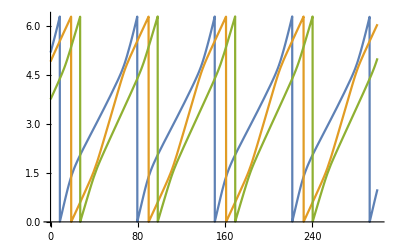

```mathematica
Plot[Evaluate@Through[GenerateAngleFunctions[4Rs,70Degree][t]],{t,0,300}]
```

## All in All Rendering --- Single Point

一个返回函数 f[t]的函数。
这个f[t]的输入是观测时间，而输出则是一个完整的Graphics图元，表示了被观测到的位置（观测点为{0,0,0}）及颜色（包括强度）

这里考虑的是一个沿着圆轨道运行的粒子，认为它是一个黑体。
R1是轨道半径, θ1,t1,γ1是三个欧拉角, θ1定义如前, t1对应ϕ1/ω,代表了时间上的offset, γ1 则代表了轨道面相对于极轴的旋转.
T0代表了原始的温度（在其他情况下可以改成任何控制颜色的参数）
I0代表了物体原本的发射强度

选项ColorFunction->cf是渲染颜色时用到的颜色函数，默认为PhysicalColor包内的TemperatureColor函数
选项ColorFunctionScaling->colorfunc是渲染颜色时用的rescale方法，默认不scale
选项IntensityFunctionScaling->intfunc是渲染强度时用的rescale方法，默认不scale

要求后面两个Rescale函数都可以作用于List。

对于一个单色光来说，颜色和强度的换算是很简单的，就是频率乘个频率因子，强度乘个强度因子就可以了，这都是前面讨论的内容。

但是这里很重要的一点是，黑体辐射是一个连续谱，其频移时在可见光波段强度分布（也就是颜色）的变化如下：
若原来颜色是color(T)，则在ν->k ν的变换下，颜色变为color(k T)
若原来强度是I(T)，则变为f(k)/k^4 I(kT)，其中f(k)为单频光强度变化因子，即前面讨论的内容。

关于这个的讨论不是很Trivial，我们来解释一下。首先看普朗克的黑体辐射定律，单位频率内能量密度为：
E(ν,T)=const*ν^3/(exp(hν/kT)-1)
由此可得：
E(λν,T)=λ^3 E(ν,T/λ)

我们来看下视明度是怎么定义的：
I(T)=∫_νmin^νmax E(ν,T)S(ν)ⅆν
其中S(ν)是视明度函数，代表了单位能量的，频率为ν的光，视明度是多少。

那在频移ν->k ν之后，我们假设能量密度函数变为了E’(ν,T)，这时明度为：
I’(T)=∫_νmin^νmax E’(ν,T)S(ν)ⅆν

考虑频率ν~ν+dν内的光，之前这段光强度为：
E(ν,T)dν，而现在其频率变为了kν~kν+kdν，强度增强为f(k)倍，即有：
f(k)E(ν,T)dν=E’(kν,T)kdν
借助这个关系我们可以化简前面的I’(T)了：
I’(T)=∫_νmin^νmax E’(ν,T)S(ν)ⅆν
         =f(k)/k∫_νmin^νmax E(ν/k,T)S(ν)ⅆν
         =f(k)/k^4∫_νmin^νmax E(ν,k T)S(ν)ⅆν
         =f(k)/k^4 I(k T)
         
完美！而且同样遵循这个过程，只不过把S(ν)换成色感的函数，我们也知道了颜色其实只是变为k T时对应的颜色而已。

```mathematica
<<PhysicalColor`
```

```mathematica
IntensityFunctionScaling::usage="Scale Intensity.";
Protect@IntensityFunctionScaling;
```

```mathematica
Options[RenderFunc]={ColorFunction->TemperatureColor,ColorFunctionScaling->(#&),IntensityFunctionScaling->(#&),"StaticObserver"->True};
```

```mathematica
RenderFunc[R1_,{θ1_,t1_,γ1_},{T0_,I0_},OptionsPattern[]]:=
Function[t,Through[#[t]]]&@Module[{
(*Velocity of observer*)
vobs=N@Sqrt[(1-Rs/R0)Rs/(2R0)],
(*list of ϕ1 parameters*)
ϕ1l=Range[0.,2Pi,1Degree],
(*Polar coordinates θ and ϕ*)
θl0,ϕl0,
(*velocity of object and its norm*)
vrl,vθl,vϕl,vnorml
},
(*Polar coordinate θ*)
θl0=ArcCos[Sin[ϕ1l]Sin[θ1]];

(*Original ϕ*)
ϕl0=ArcTan[Cos[ϕ1l],Sin[ϕ1l]Cos[θ1]]+γ1;

(*velocity of object*)
vrl=ConstantArray[0,Length@ϕ1l];
vθl=-(Cos[ϕ1l]Sin[θ1])/Sqrt[1 - Sin[θ1]^2Sin[ϕ1l]^2]*Sqrt[Rs/(2R1^3)];
vϕl=1/(Cos[ϕ1l]^2/Cos[θ1]+Cos[θ1]Sin[ϕ1l]^2)*Sqrt[Rs/(2R1^3)];

(*velocity norm*)
vnorml=Calcβ[{R1,θl0,0},{vrl,vθl,vϕl}];

MapThread[Module[{
(*Observed ϕ1 parameter - t*)
ϕ1t=#3,
(*actual θ of object*)
θl=#1,
(*angle between velocy and ray*)
cosl=#4,
(*Observed values - ϕ1*)
(*Geometry*)
θobsl,ϕobsl=ϕl0+#2,
(*Frequency and intensity shift*)
freqobsl,intobsl,
(*helper function*)
helpf
},
θobsl=ReceiveAngleFunction[R1,θl];

(*Frequency*)
freqobsl=FrequencyMult[R1,vnorml,cosl];

(*Process with the non-static observer*)
If[OptionValue["StaticObserver"]=!=True,
Module[{θtransl,ϕtransl,δ=ArcSin[vobs]},
(*Geometrics, static frame*)
θtransl=ArcCos[Sin[θobsl]Cos[ϕobsl]];
ϕtransl=ArcTan[Sin[θobsl]Sin[ϕobsl],Cos[θobsl]];
(*Frequency shift due to movement of observer, intensity shift is calculated together later*)
freqobsl*=(1+vobs Cos[θtransl])/Sqrt[1-vobs^2];
(*Angle shift due to movement of observer*)
θtransl=ArcCos[(vobs+Cos[θtransl])/(1+vobs Cos[θtransl])];
(*Transform back*)
(*Here we change the center of viewing angle so that the black hole's center is at {0,0}*)
θobsl=ArcCos[Sin[δ]Cos[θtransl]+Cos[δ]Sin[θtransl]Sin[ϕtransl]];
ϕobsl=ArcTan[Cos[δ]Cos[θtransl]-Sin[δ]Sin[θtransl]Sin[ϕtransl],Sin[θtransl]Cos[ϕtransl]]
]
];

ϕobsl=Catenate[MapIndexed[#1+2Pi#2[[1]]&,Split[ϕobsl,Less]]];

(*Intensity*)
intobsl=freqobsl^2*IntensityFunction1[R1,θl]*IntensityMult2[vnorml,cosl]*TemperatureIntensity[freqobsl T0]/TemperatureIntensity[T0]/freqobsl^4;

(*Helper function to construct interpolating functions*)
helpf[l_]:=Interpolation[Thread[{ϕ1l,l}]];

With[{
cf=OptionValue[ColorFunction],
(*Interpolating functions*)
t11=t1,
ϕ1f=#3,
θfunc=helpf[θobsl],
ϕfunc=helpf[ϕobsl],
freqfunc=helpf[OptionValue[ColorFunctionScaling][T0 freqobsl]],
intfunc=helpf[OptionValue[IntensityFunctionScaling][I0 intobsl]]
},
 
(*Final function*)
Function[t,
With[{ϕ11=ϕ1f[t+t11]},
{Append[cf[freqfunc[ϕ11]],intfunc[ϕ11]],
With[{θ=θfunc[ϕ11],ϕ=ϕfunc[ϕ11]},
(*Point[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}]*)Point[Tan[θ]{Cos[ϕ],Sin[ϕ]}]]}
]]
]
]&,{{θl0,2Pi-θl0,2Pi+θl0},{0,Pi,0},GenerateAngleFunctions[R1,θ1],CalcCosAngle[{R1,θl0,0},{vrl,vθl,vϕl}]}]]
```

内置的Rasterize的最大问题是很难处理好低亮度区域，会显著地损失掉颜色的位数。为了实现后期的亮度变换，我们只能勉为其难的生成一组照片（这里两张就够了，比较幸运），其中第二张相比于前一组亮度被提升了16倍，这样就可以分级调节，实现HDR效果。
这段代码中无关部分耗时约2s，其实还是可以忍受的。

```mathematica
HDRRasterize[gr_Graphics,convertfunc_,opts:OptionsPattern[Rasterize]]:=
Module[{rasterl=Join[ColorSeparate[ColorConvert[Rasterize[gr,opts],"HSB"]],ColorSeparate[ColorConvert[Rasterize[gr/.RGBColor[r_,g_,b_,op_]:>RGBColor[r,g,b,16 op],opts],"HSB"]]],mask,invmask},
mask=Binarize[rasterl[[3]],1/16];
invmask=1-mask;
ColorCombine[{
mask*rasterl[[1]]+invmask*rasterl[[4]],
mask*rasterl[[2]]+invmask*rasterl[[5]],
mask*convertfunc[rasterl[[3]]]+invmask*convertfunc[rasterl[[6]]/16.]},"HSB"]
]
```

```mathematica
npts=5000;
rflist=MapThread[Function[{R1,θ1,t1,γ1,T0,I0},RenderFunc[R1,{θ1,t1,γ1},{T0,I0},"StaticObserver"->False(*,IntensityFunctionScaling->(.7(#/.5)^0.5&)*)]],
{RandomReal[{3,4.5},npts],
RandomReal[-{83,86}Degree,npts],
RandomReal[{0,10000},npts],
RandomReal[15Degree+{-2,2}Degree,npts],
RandomReal[{4000,10000},npts],
RandomReal[{.03,.1},npts]
}
];
```

```mathematica
g=Graphics[{(*AbsolutePointSize@.1,White,Point[{Sin[20Degree]Cos[#],Sin[20Degree]Sin[#],Cos[20Degree]}&/@Range[0.,360.Degree,60.Degree]],*)AbsoluteThickness@2,Map[Line[#[[;;,2,1]],VertexColors->MapThread[Function[{col,len,mult},MapAt[mult^2*#*0.006/len&,col,4]],{#[[;;,1]],Prepend[#,#[[1]]]&@BlockMap[Norm[#[[2]]-#[[1]]]&,#[[;;,2,1]],2,1],Subdivide[Length[#]-1]}]]&,Reverse@Transpose[Through[rflist[#]]&/@(Range[0,3,.1]),{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}];
```

无Gamma修正（像素值是亮度）

```mathematica
Rasterize[g,ImageSize->{1920,1080}/5]
```

Gamma修正（看屏幕看到的亮度是实际亮度）

```mathematica
HDRRasterize[g,#^(1/2.2)&,ImageSize->{1920,1080}]
```

-Graphics-

-Graphics-

```mathematica
Clear@g
```

#### Parallel

```mathematica
tlist=Range[0,20,.05];

CloseKernels[];
LaunchKernels@8;
ParallelEvaluate[<<PhysicalColor`];
SetSharedVariable[count];
SetSharedVariable[tlist]

count=0;
Dynamic[Row[{count,"/",Length@tlist}]]
ProgressIndicator[Dynamic[count/Length@tlist]]
Dynamic[Row[{"Time Left: ",(Now-tstart)*(Length@tlist-count)/count}],TrackedSymbols:>{count}]
```

```mathematica
tstart=Now;
count=0;
With[{nbdir=NotebookDirectory[]},
ParallelDo[
Export[nbdir<>"IMG\\T_"<>IntegerString[num,10,3]<>".png",HDRRasterize[Graphics[{AbsoluteThickness@2,Map[Line[#[[;;,2,1]],VertexColors->MapThread[Function[{col,len,mult},MapAt[mult^2*#*0.006/len&,col,4]],{#[[;;,1]],Prepend[#,#[[1]]]&@BlockMap[Norm[#[[2]]-#[[1]]]&,#[[;;,2,1]],2,1],Subdivide[Length[#]-1]}]]&,Reverse@Transpose[Through[rflist[#]]&/@(tlist[[num]]+Range[0,3,.1]),{3,2,1}],{2}]},Background->Black,ImageSize->{500,Automatic},PlotRange->{{-1.28,1.28},{-0.72,0.72}}],#^(1/2.2)&,ImageSize->{1920,1080},ImageResolution->72]];
count++,{num,Length@tlist}
]]//AbsoluteTiming
```

{13331.1,Null}